# Dodelson Chap 3 Ex 7

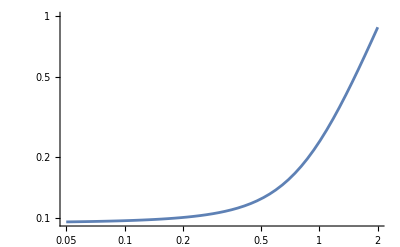

```mathematica
tn:= 886.7 (*neutron half life*)
H:=1.13 (*radiation-dominated era*)
Q:= 1.293  (*mass difference of neutron and proton(in MeV)*)
G:=0.015
g:=10.75

rho[x_]:=255/(tn x^5)(12+6x+x^3)(*neutron-proton conversion rate*)
miu[x_]:= -255/(tn Q)((4Pi^3 G Q^2 g)/45)^(-1/2)((4/x^3+3/x^2+1/x)+(4/x^3+1/x^2)Exp[-x]-(4/initial^3+3/initial^2+1/initial)+(4/initial^3+1/initial^2)Exp[-initial])
X[T_]:=NIntegrate[(rho[y]Exp[-y])/(y H)Exp[miu[y]-miu[Q/T]],{y,initial,Q/T}]
initial:=0.0001 
plotA=LogLogPlot[X[T],{T,0.05,2}]
```

### To get the correct G:

```mathematica
Solve[((4Pi^3 t Q^4)/45 10.75)^(1/2)==1.13,t]
```

{{t→0.015419}}

### X_EQ

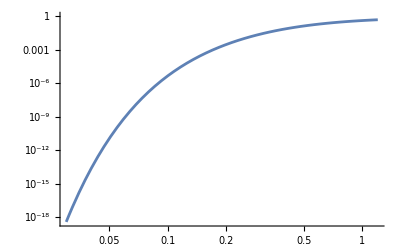

```mathematica
XEQ[x_]:= 1/(1+Exp[Q/x])
plotB=LogLogPlot[2 XEQ[x],{x,0.03,1.2}, PlotLegends->"EQ"]
```

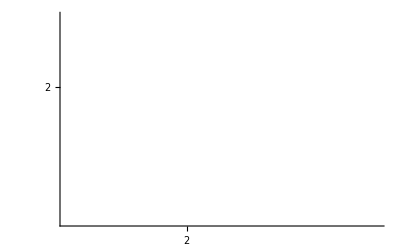

```mathematica
Show[plotA,plotB,Ticks->{{0.01,0.1,1},{10^-5,10^-4,10^-3,10^-2,10^-1,1}},PlotRange->{{0.5,1},{0.1,1}}](*Not working, scale decoupling*)
```

### Use Overlay:

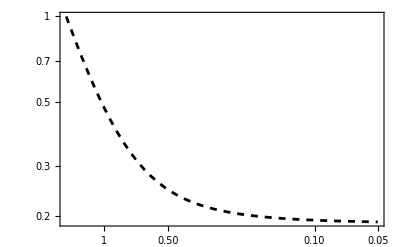
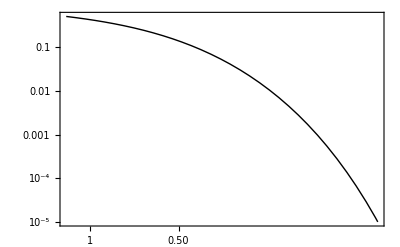

```mathematica
Overlay[{LogLogPlot[2X[T],{T,0.05,2},PlotRange->{{0.03,1.1},{10^-5,1}},ScalingFunctions->{"Reverse",None},Ticks->Automatic,PlotStyle->{Dashed,Black},Frame->True],
LogLogPlot[ 2XEQ[x],{x,0.03,1.2},PlotRange->{{0.03,1.1},{10^-5,1}},ScalingFunctions->{"Reverse",None},Ticks->Automatic, PlotStyle->{Black,Thin},Frame->True]}]
```